```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
ClearAll[AnsatzLocal, AnsatzNoLocal, ConoCausal, ColumnasCircuito,
    MetricasConoCausal, DiagramaConoCausal, MostrarConoCausal]

capas[listas_] := Catenate @ Riffle[listas, {{"Barrier"}}]

AnsatzLocal[n_Integer, params_List] := QuantumCircuitOperator[
    capas @ {
        Table["RY"[params[[j]]] -> j, {j, n}],
        Table["CZ" -> {j, j + 1}, {j, 1, n - 1, 2}],
        Table["CZ" -> {j, j + 1}, {j, 2, n - 1, 2}],
        Table["RY"[params[[n + j]]] -> j, {j, n}]
    },
    "Parameters" -> params
]

AnsatzNoLocal[n_Integer, params_List] := QuantumCircuitOperator[
    capas @ {
        Table["RY"[params[[j]]] -> j, {j, n}],
        Table["CZ" -> {j, j + Floor[n / 2]}, {j, Floor[n / 2]}],
        Table["RY"[params[[n + j]]] -> j, {j, n}]
    },
    "Parameters" -> params
]

soportes[qc_] := Union @@ #["Order"] & /@ qc["Operators"]

retroceder[{cono_, puertas_}, {i_, sop_}] := If[IntersectingQ[sop, cono],
    {Union[cono, sop], Prepend[puertas, i]},
    {cono, puertas}
]

ConoCausal[qc_QuantumCircuitOperator, obs : {__Integer}] := AssociationThread[{"Qubits", "Puertas"},
    Fold[retroceder, {Union[obs], {}}, Reverse @ MapIndexed[{First[#2], #1} &, soportes[qc]]]
]

apilar[{reloj_, piso_, columnas_}, "Barrier" | "Barrier"[___]] :=
    {<||>, Max[piso, Values[reloj], 0] + 1, columnas}

apilar[{reloj_, piso_, columnas_}, op_] := With[{tramo = Range @@ MinMax[Union @@ op["Order"]]},
    With[{c = Max[piso, Lookup[reloj, tramo, 0]] + 1},
        {Join[reloj, AssociationThread[tramo -> c]], piso, Append[columnas, c]}
    ]
]

ColumnasCircuito[qc_QuantumCircuitOperator] := Last @ Fold[apilar, {<||>, 0, {}}, qc["Elements"]]
```

```mathematica
MetricasConoCausal[qc_QuantumCircuitOperator, obs : {__Integer}] := Module[
    {cono = ConoCausal[qc, obs], columnas = ColumnasCircuito[qc], n = qc["Width"]},
    Dataset @ <|
        "Observable" -> obs,
        "Qubits totales" -> n,
        "Qubits en el cono" -> cono["Qubits"],
        "Tamano del cono" -> Length[cono["Qubits"]],
        "Fraccion del sistema" -> N[Length[cono["Qubits"]] / n],
        "Radio espacial" -> Max[Abs @ Outer[Subtract, cono["Qubits"], obs]],
        "Puertas en el cono" -> Length[cono["Puertas"]],
        "Puertas totales" -> Length[columnas],
        "Profundidad efectiva" -> Length @ Union @ columnas[[cono["Puertas"]]],
        "Profundidad total" -> Length @ Union @ columnas
    |>
]

soporteColumnas[qc_QuantumCircuitOperator, obs : {__Integer}] := Module[
    {cono = ConoCausal[qc, obs], columnas = ColumnasCircuito[qc], sop = soportes[qc], porColumna},
    porColumna = GroupBy[cono["Puertas"], columnas[[#]] &, Union @@ sop[[#]] &];
    Reverse @ Rest @ FoldList[
        Union[#1, Lookup[porColumna, #2, {}]] &,
        Union[obs],
        Reverse @ Range @ Max[columnas]
    ]
]

aristas[{c_, q_}] := Partition[
    {{c - 1/2, -q - 1/2}, {c + 1/2, -q - 1/2}, {c + 1/2, -q + 1/2}, {c - 1/2, -q + 1/2}, {c - 1/2, -q - 1/2}},
    2, 1
]

contorno[celdas_] := First /@ Select[GatherBy[Catenate[aristas /@ celdas], Sort], Length[#] == 1 &]

$colorCono = RGBColor[0.82, 0.18, 0.18];
$fondoCono = Directive[$colorCono, Opacity[0.3]];
$bordeCono = Directive[AbsoluteThickness[1.6], $colorCono];
$fondoFuera = Directive[GrayLevel[0.55], Opacity[0.09]];
$bordeFuera = Directive[AbsoluteThickness[1], GrayLevel[0.74]];

resaltar[op_] := QuantumOperator[op, "Label" -> Replace[op["Label"], {
    Subscript["C", sub_][ctrl1_, ctrl0_] :> Subscript["C", Row[{sub}]][ctrl1, ctrl0],
    etiqueta_ :> Row[{etiqueta}]
}]]
```

```mathematica
DiagramaConoCausal[qc_QuantumCircuitOperator, obs : {__Integer}, opts : OptionsPattern[Graphics]] := Module[
    {cono = ConoCausal[qc, obs], columnas = ColumnasCircuito[qc], diagrama, celdas, derecha},
    diagrama = QuantumCircuitOperator[
        MapAt[resaltar, qc["Elements"],
            List /@ Flatten[Position[qc["Elements"], _QuantumOperator, {1}]][[cono["Puertas"]]]],
        "Parameters" -> qc["Parameters"]
    ]["Diagram",
        "GateBackgroundStyle" -> {_Row -> $fondoCono, _ -> $fondoFuera},
        "GateBoundaryStyle" -> {_Row -> $bordeCono, _ -> $bordeFuera}
    ];
    celdas = Catenate @ MapIndexed[Thread[{First[#2], #1}] &, soporteColumnas[qc, obs]];
    derecha = Last @ First @ PlotRange[diagrama];
    Show[
        diagrama,
        Graphics[{
            {$colorCono, Opacity[0.07], EdgeForm[None],
                Rectangle[{#1 - 1/2, -#2 - 1/2}, {#1 + 1/2, -#2 + 1/2}] & @@@ celdas} /. Max[columnas] + 1/2 -> derecha,
            {$bordeCono, Dashing[{0.007, 0.007}], Line /@ contorno[celdas]} /. Max[columnas] + 1/2 -> derecha,
            {$colorCono, Disk[{derecha, -#}, 0.1], Text[Style["O", 14, Bold, $colorCono], {derecha + 0.4, -#}]} & /@ obs
        }],
        opts,
        PlotRange -> All
    ]
]

MostrarConoCausal[qc_QuantumCircuitOperator, obs : {__Integer}, opts : OptionsPattern[Graphics]] := Grid[
    {{DiagramaConoCausal[qc, obs, opts], MetricasConoCausal[qc, obs]}},
    Alignment -> Center, Spacings -> 2
]
```

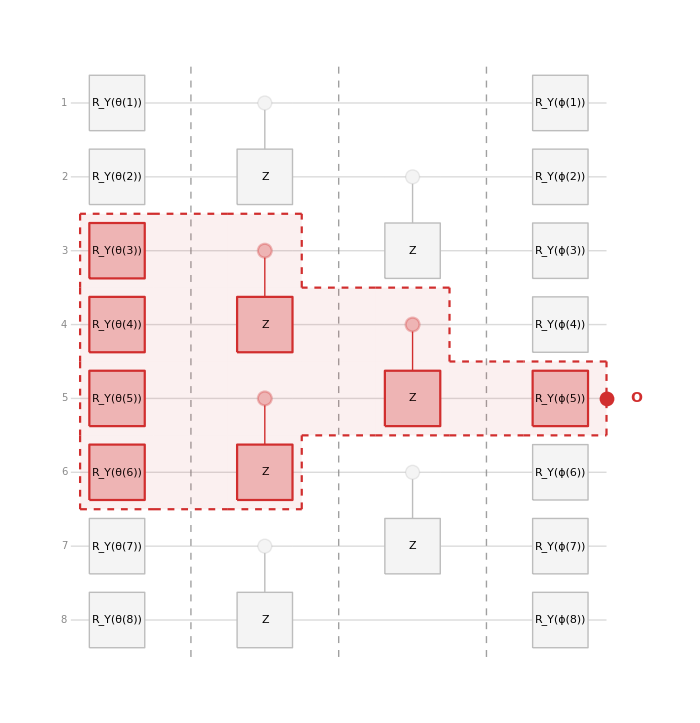
-Graphics- |

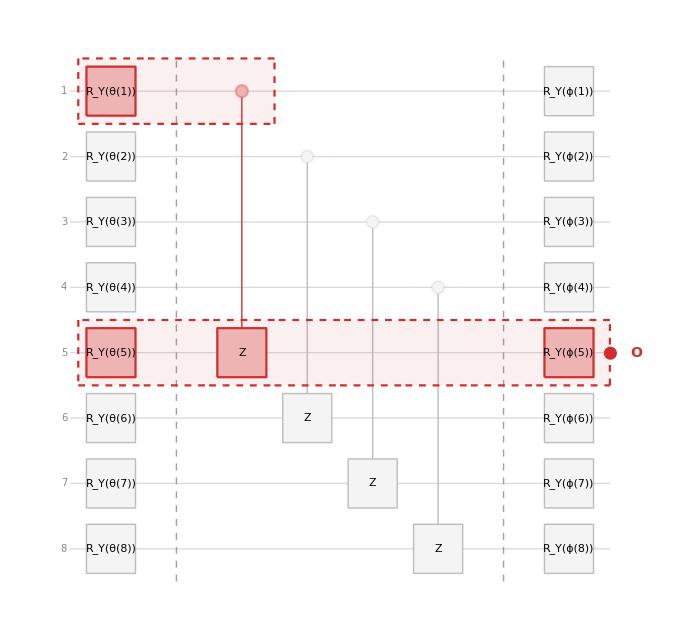
-Graphics- |

```mathematica
params8=Join[Array[θ,8],Array[ϕ,8]];
local=AnsatzLocal[8,params8];
noLocal=AnsatzNoLocal[8,params8];

MostrarConoCausal[local,{5},ImageSize->700]
MostrarConoCausal[noLocal,{5},ImageSize->700]
```